# DarkModeEverything

## By: Tone

## Introduction

## Description

The aim of this project is to have a complete dark mode throughout all of Mathematica and its various components that does not restrict any features or functionality. Whilst the project has not yet reached 100% coverage, it far exceeds the coverage of all other dark themes publicly available, and has almost no known functionality constraints. The project has also evolved to include general front end functionality extensions and improvements.

## Instructions

### 1. Backup

Prior to installation, you should backup your “SystemFiles” folder inside “$InstallationDirectory”.

#### DME Palette

#### Manual

### 2. Replace existing files

Replace the existing files inside “$InstallationDirectory/SystemFiles” with the ones found inside “DarkModeEverything/SystemFiles”.

#### DME Palette

#### Manual

### 3. Install Fonts

Install AnnonymousPro font.

#### DME Palette

#### Manual

### 4. Set defaults

Set DarkModeEverything.nb as the default global StyleDefinitions

#### DME Palette

#### Manual

### 5. Install Rectify11

Some elements inside of Mathematica, like buttons, menu bars, scrollbars and so on are controlled by the OS. As such, if using windows, custom OS themes need to be installe . This is made easy by Rectify11 which handles all of this for you.

For Linux, a custom Qt file can be passed to Mathematica to control the color of OS controlled elements.

## Cell Styles

This section lists examples of most commonly used cell styles including any shortcuts used to generate one.

Key:

CellStyle [ shortcut1 | shortcut2 ]- “ [ ] ” contain different shortcuts separated by “ | ” to generate a cell .

Shortcuts can take 2 main forms:

Alt + NumberRowKey

NumberRowKey is a number from the keyboards number row

Eg. Style1 [ Alt + Num ]:
	Pressing Alt+Num inside any cell will change that cell to Style1
	(Or generate a new Style1 cell if cell insertion line is selected)

CellStyle + Key

CellStyle is an existing cell style

Key is any keyboard key

Eg. Style1 [ Style2 + Key ],
	Pressing Key inside a cell of style Style2 will change that cell into a Style1 cell

Note: Any [ Input + Key ] shortcut will work when inputting a new cell in the cell insertion line.

## Examples

# Title [ Alt+1 ]

## Subtitle [ Alt+2 ]

## Chapter [ Alt+3 ]

## Section [ Alt+4 ]

### Subsection [ Alt+5 ]

#### Subsubsection [ Alt+6 ]

##### Subsubsubsection

Text [ Alt + 7 ]

Item [ Text+Tab | Text+* | Subitem+Backspace ]

Subitem [ Item+Tab | Item+* | Subsubitem+Backspace ]

Subsubitem [ Subitem+Tab | Subitem+* ]

```mathematica
"Code [ Alt+8 | Input+` ]"
```

"InitialisationCell [ Code+Tab ]";

```mathematica
"Input [ Alt+9 | Code+` ]"
```

MSG::example: Message

Print

PrintTemporary

EchoBefore

EchoAfter

Echo

EchoTiming

Output

Purple delimiter [ Input+- ]

ExternalLanguage [ Input+> ]

NLInput [ Input+= ]

WolframAlphaInput [ NLInput+= ]

## Example outputs

## Entities

```mathematica
Quantity[12, "Meters"]
```

```mathematica
Entity["Country","UnitedKingdom"][EntityProperty["Country","AdministrativeDivisions"]]
```

```mathematica
EntityClass["Country","EuropeanUnion"][EntityPropertyClass["Country","EconomicProperties"]]
```

## Dataset

```mathematica
ExampleData[{"Dataset","Planets"}]
```

## Plots

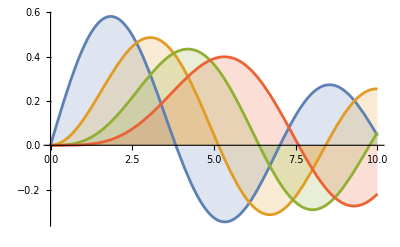

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

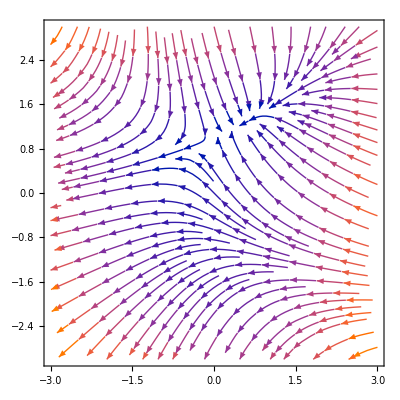

```mathematica
StreamPlot[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3}]
```

```mathematica
DiscretePlot3D[{PDF[MultivariatePoissonDistribution[3,{1,1}],{t,u}],PDF[MultivariatePoissonDistribution[5,{2,2}],{t,u}]},{t,0,10},{u,0,10},ExtentSize->Full]
```

-Graphics3D-

## Manipulate

```mathematica
Manipulate[]
```

## NaturalLanguageInput

WolframAlphaQueryParseResults

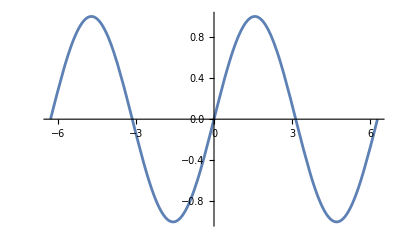

## WolframAlpha

Denmark

WolframAlphaQueryResults

## Context coloring

DME has implemented different font coloring depending on the context of a symbol as shown below:

```mathematica
Undefined`Symbols
System`Symbol
Global`Symbols
Other`Symbols
```

#### Initialisation

Other`Symbols = 0;
Global`Symbols= 0;

## Extended coverage

## Documentation

The documentation is completely covered by this dark theme’s custom Reference.nb stylesheet. The styling uses the same design language as the main notebooks and restricts NO functionality, covering all sections of the documentation.

The following hyperlinks showcase some of the changes to the different documentation sections:

Function documentation

Entity documentation

Tech Notes

Monographs

## Toolbars

All built in WindowToolbars are covered by this dark theme.

## Message window

The Mathematica message window has also been changed according to the dark theme.

```mathematica
(*
	Evaluation of this cell generates a
	message inside the message window
*)
SessionSubmit[
	1/0
];
```

## Wolfram Chatbooks

DME comes with a dark Chatbook.nb stylesheet.

```mathematica
CreateNotebook["ChatEnabled"];
```

## Testing notebooks

DME comes with a dark MUnit.nb stylesheet used in testing notebooks.

```mathematica
CreateNotebook["Testing"];
```

## Stylesheet theming

DME comes with a dark StylesheetFormatting.nb stylesheet which changes the theming of the stylesheet editor notebooks.

```mathematica
SystemOpen@
FileNameJoin[{$InstallationDirectory,"SystemFiles","FrontEnd","StyleSheets","DarkModeEverything.nb"}]
```

## Handy changes & additions

## Customization tools

DME comes with a custom init.m file which defiles helper functions and global style variables that can be changed by the user to customise the look of DME.

#### SetAccentColor

SetAccentColor is a function which can be used to change the main accent color of DME from which all other colors are derived. For example:

```mathematica
SetAccentColor[Hue[0.9,.8, 0.9]]
```

Hue[0.9, 0.8, 0.9]

Or we can also set back to the default DME accent color:

```mathematica
SetAccentColor[Default]
```

Hue[0.47, 0.6, 0.75]

## NotebookAutoSave

The DME stylesheet enablesNotebookAutoSave which will attempt to save the notebook any time an evaluation is performed. This can give an error sound when evaluating a notebook which is not yet been saved, however, this does not impact functionality.

## ResetOptions

ResetOptions is a function which handles the applying of all changes to default function options required by DME. Some functions, when evaluate can change these back to defaults and so evaluating ResetOptions is an easy way to get back to the DME defaults:

```mathematica
ResetOptions[]
```

We can also reset all options back to Automatic by using:

```mathematica
ResetOptions[Automatic]
```

## Map subscript level-spec

This is a shorthand implemented in the initialisation of the DME stylesheet to allow for quick level specification to Map’s “/@” abbreviation:

```mathematica
(* f(/@)_i list -> Map[f, list, {i}] *)
f (/@)_2 {1,1,{2,{3,3}}}
```

{1,1,{f[2],f[{3,3}]}}

## Outstanding items & known issues

As mentioned in the description, this project is very close to complete dark theme coverage within Mathematica, successfully, there are still some components that have yet to be successfully changed.
This could be due to either it being too difficult to make the changes, or more commonly, I didn’t quite get to them yet.
This section will list the biggest outstanding items:

The stack trace window in messages is one of the only components which is functionally effected by this theme. The background is still light while font color is also light, resulting in unreadable text. This is solved by using the “Pop out” button, however, this is the primary current TODO.

Package files (.wl & .m) seems to not like the editing of Code and InitilisationCell cells and so they currently will comment all code out if saved through Mathematica. I tend to use IDE’s like VSCode for package files however this issue is one that is being worked on. For now, the default stylesheets can be used for scripts and packages.

The background of the workflow guides docked cell inside the documentation is still in a light theme. I have tried to track down the style of this docked cell to no avail. This one annoys me a lot and is one of the primary current TODOs although it is still perfectly usable.

WolframAlphaPod text on labels and plot axes are still not coherently themed. These font colors are handled inside the WolframAlphaClient.m source file and not through any StyleSheet defaults and as such, take a lot of time to track down and change. Since these colors do not impair usability, and more importantly, almost never use WolframAlphaInput, so these are on the “I should probably change these... some day” box.